# 4 - answer to challenge

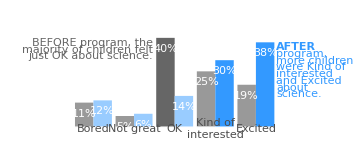

```mathematica
genLines[lines_, startPt_, spacing_, anchor_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, anchor],
		  opts], {n, 0, Length[lines]-1}]

tintedColour[colour_, intensity_] := 
	Apply[RGBColor, (1-colour)*(1-intensity) + colour]

defaultBlue = tintedColour[{0,0.5,1}, 0.4];
hlBlue = tintedColour[{0,0.5,1}, 0.8];
defaultGray = GrayLevel[0.6];
hlGray = GrayLevel[0.4];

textBefore = {Row[{Style["BEFORE", Bold], " program, the"}],
			  "majority of children felt",
			  "just OK about science."};

textAfter = {Style["AFTER",Bold],
			 "program,",
			 "more children",
			 "were Kind of",
			 "interested",
			 "and Excited",
			 "about",
			 "science."};

dataBefore = {11, 5, Style[40, hlGray], 25, 19, 0};
dataAfter = {12, 6, 14, Style[30, hlBlue], Style[38, hlBlue], 0};
labels = {"Bored", "Not great", "OK", "Kind of\ninterested", "Excited", ""};
stLabels = Map[Style[#, GrayLevel[0.3]]&, labels];

BarChart[Transpose[{dataBefore, dataAfter}],
	ChartLabels->{stLabels, None},
	LabelingFunction->(Placed[Style[Row[{#,"%"}], White], Top]&),
	ChartStyle->{Directive[defaultGray,EdgeForm[None]], 
	            Directive[defaultBlue,EdgeForm[None]]},
	PlotLabel->"\n\n",
	BarSpacing->{0,0.2},
	Axes->{True,False},
	AxesStyle->White,
	AspectRatio->1.0/2.4,
	PlotRangeClipping->False,
	
	Epilog->{
		hlGray,
		genLines[textBefore, {4.8,40}, 3, {1,1}, FontSize->11],
		
		hlBlue,
		genLines[textAfter, {11.5,38}, 3, {-1,1}, FontSize->11],
		
		GrayLevel[0.2],
		Style[Text["How do you feel about science?", {0.4,48}, {-1,-1}],
		           FontSize->16]
	}
]
```

## An alternative solution: building the graph from scratch

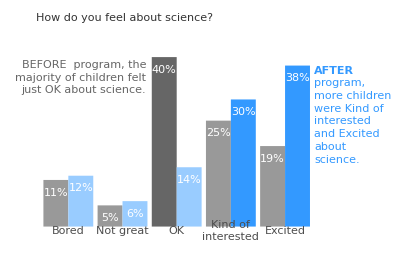

```mathematica
genLines[lines_, startPt_, spacing_, offset_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, offset],
		  opts], {n, 0, Length[lines]-1}]

tintedColour[colour_, intensity_] := 
	Apply[RGBColor, (1-colour)*(1-intensity) + colour]

defaultBlue = tintedColour[{0,0.5,1}, 0.4];
hlBlue = tintedColour[{0,0.5,1}, 0.8];
defaultGray = GrayLevel[0.6];
hlGray = GrayLevel[0.4];

textBefore = {Style["BEFORE", Bold] " program, the",
			  "majority of children felt",
			  "just OK about science."};

textAfter = {Style["AFTER",Bold],
			 "program,",
			 "more children",
			 "were Kind of",
			 "interested",
			 "and Excited",
			 "about",
			 "science."};
			 
dataBefore = {11, 5, 40, 25, 19};
dataAfter = {12, 6, 14, 30, 38};
labels = {"Bored", "Not great", "OK", "Kind of\ninterested", "Excited"};
stLabels = Map[Style[#, GrayLevel[0.3]]&, labels];

(* drawing the bars *)
boxFracWidth = 0.46;
groupWidth = 15;
beforeBoxes = Table[Rectangle[{groupWidth n,0},
			                  {groupWidth(n+boxFracWidth), dataBefore⟦n+1⟧}],
			        {n, 0, Length[dataBefore]-1}];
beforeBoxes⟦3⟧ = Style[beforeBoxes⟦3⟧, hlGray];

afterBoxes  = Table[Rectangle[{groupWidth(n+boxFracWidth),0},
			                  {groupWidth(n+2 boxFracWidth), dataAfter⟦n+1⟧}],
			        {n, 0, Length[dataAfter]-1}];
afterBoxes⟦4⟧ = Style[afterBoxes⟦4⟧, hlBlue];			 
afterBoxes⟦5⟧ = Style[afterBoxes⟦5⟧, hlBlue];			 

(* drawing the labels *)
beforeLabels = Table[Style[Text[Row[{dataBefore⟦n+1⟧, "%"}],
                                {groupWidth(n+boxFracWidth/2), dataBefore⟦n+1⟧-3}],
                           White, FontSize->11.5],
                     {n, 0, Length[dataBefore]-1}];
afterLabels = Table[Style[Text[Row[{dataAfter⟦n+1⟧, "%"}],
                                {groupWidth(n+3boxFracWidth/2), dataAfter⟦n+1⟧-3}],
                          White, FontSize->11.5],
                    {n, 0, Length[dataAfter]-1}];
horizontalLabels = Table[Style[Text[labels⟦n+1⟧,
                                    {groupWidth(n+boxFracWidth), -1},
                                    {0,1}],
                               GrayLevel[0.3], FontSize->11.2],
                         {n, 0, Length[labels]-1}];

Graphics[{
	{defaultGray, EdgeForm[None], beforeBoxes}, 
	{defaultBlue, EdgeForm[None], afterBoxes},
	beforeLabels, afterLabels, horizontalLabels,
	
	hlGray,
	genLines[textBefore, {1.9groupWidth,37}, 3, {1,-1}, FontSize->11],	
	hlBlue,
	genLines[textAfter, {5groupWidth,38}, 3, {-1,1}, FontSize->11],
	
	(* title *)
	GrayLevel[0.2],
	Style[Text["How do you feel about science?", {-2,48}, {-1,-1}],
	           FontSize->16]
	
}]
```